```mathematica
Quit[];
Clear["Global`*"]
```

```mathematica
Import["/Users/conordyson/Documents/GitHub/BHPT/KerrGeodesics/KerrGeodesicsTest/Kernel/KerrGeoPlunge.m"];
```

## ISSO Testing

### Setting Up ISSO

```mathematica
a =0.5;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a, "ISSORadialParam",5];
{RI,R4} = orbit["RadialRoots"][[3;;]];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{KR,KZ} = orbit["EllipticBasis"];
z[λ_] = Cos[θ[λ]];
{ϵ,L,Q} = orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];
```

### ISSO Plots

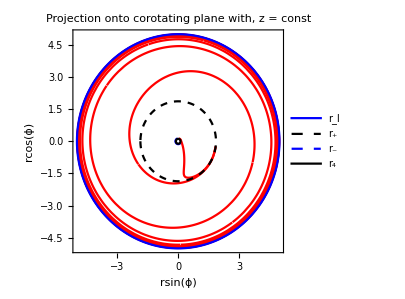
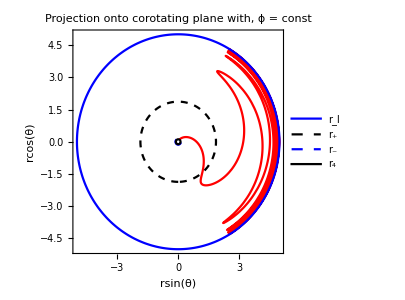

corotatingISSOPlots.pdf

```mathematica
v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]],Re[r[λ]]Cos[Re[ϕ[λ]]]}, {λ,0,20},ImageSize->300, PlotRange->All,PlotLabel-> Style["Projection onto corotating plane with, z = const",Black,14], PlotStyle->Red, MaxRecursion->10,Frame->True,FrameLabel->{ Style["rsin(ϕ)",Black,14], Style["rcos(ϕ)",Black,14]}];
v2 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,PlotRange->All,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotLegends->{ Style["r_I",Black,14], Style["r_+",Black,14], Style["r_-",Black,14], Style["r_4",Black,14]}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{r[λ]*Sin[θ[λ]],r[λ]*Cos[θ[λ]]} , {λ,0,20},ImageSize->300, PlotRange->All,PlotLabel-> Style[ "Projection onto corotating plane with, ϕ = const",Black,14],MaxRecursion->10, PlotStyle->Red,Frame->True,FrameLabel->{ Style["rsin(θ)",Black,14], Style["rcos(θ)",Black,14]}];
Q2 = ParametricPlot[{{RI*Cos[π/2-u],RI Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{R4*Cos[π/2-u],R4 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,PlotLegends->{ Style["r_I",Black,14], Style["r_+",Black,14], Style["r_-",Black,14], Style["r_4",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];
corotatingISSOPlots = Row[{a1,a2}]
Export["corotatingISSOPlots.pdf",Style[corotatingISSOPlots,LineBreakWithin->False],"PDF"]
```

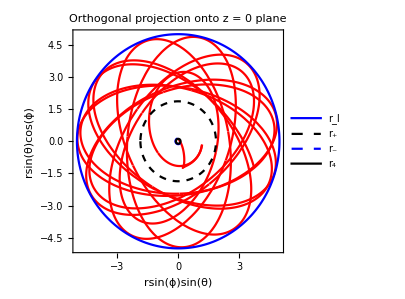
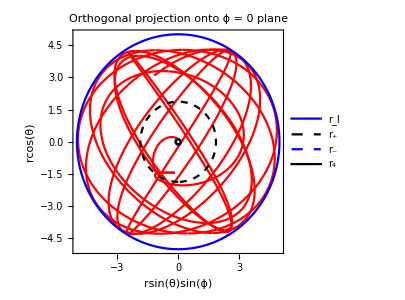
-Graphics--Graphics3D--Graphics-

ISSOPlots.pdf

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,0,20}, PlotLabel-> Style["3D Spatial Plot",Black,14],ImageSize->300,MaxRecursion->10, PlotStyle->Red,PlotRange->All, AxesLabel->{Style["rsin(ϕ)sin(θ)",Black,12],Style["rsin(θ)cos(ϕ)",Black,12],Style["rcos(θ)",Black,12]}, LabelingSize->30];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
a0 = Show[P1,P2];

v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]]}, {λ,0,20},ImageSize->300, PlotRange->All, PlotLabel->Style[ "Orthogonal projection onto z = 0 plane",Black,14], PlotStyle->Red, MaxRecursion->10, Frame->True, FrameLabel->{Style["rsin(ϕ)sin(θ)",Black,14],Style["rsin(θ)cos(ϕ)",Black,14]}];
v2 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,MaxRecursion->10,PlotRange->All,PlotLegends->{Style["r_I",Black,14],Style["r_+",Black,14],Style["r_-",Black,14],Style["r_4",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]} , {λ,0,20},ImageSize->300, PlotRange->All, PlotStyle->Red,MaxRecursion->10, PlotLabel-> Style["Orthogonal projection onto ϕ = 0 plane",Black,14],Frame->True, FrameLabel->{Style["rsin(θ)sin(ϕ)",Black,14],Style["rcos(θ)",Black,14]}, MaxRecursion->10];
Q2 = ParametricPlot[{{RI*Cos[π/2-u],RI Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{R4*Cos[π/2-u],R4 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,PlotLegends->{Style["r_I",Black,14],Style["r_+",Black,14],Style["r_-",Black,14],Style["r_4",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];


ISSOPlots = Row[{a1,a0,a2}]
Export["ISSOPlots.pdf",Style[ISSOPlots,LineBreakWithin->False],"PDF"]
```

## Generic Testing

### Setting Up Generic

```mathematica
a =0.95;
ϵ = 0.9;
L = 0.4;
Q = 8;
M=1;
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
orbit = KerrGeoPlunge[a,{ϵ,L,Q}]
{r1,r2,r3,r4} = orbit["RadialRoots"]
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{KR,KZ} = orbit["EllipticBasis"];
z[λ_]:= Cos[θ[λ]];
```

KerrGeoPlungeFunction[…]

{0.595675,4.79297,2.56884-2.59052 ⅈ,2.56884+2.59052 ⅈ}

### Generic Plots

```mathematica
Plot[2 Sin[x],{x,0,10},Frame->True,FrameLabel->{x,y},PlotLabel->2 Sin[x],LabelStyle->Directive[Red,FontFamily->"Helvetica"],FrameStyle->Green]
```

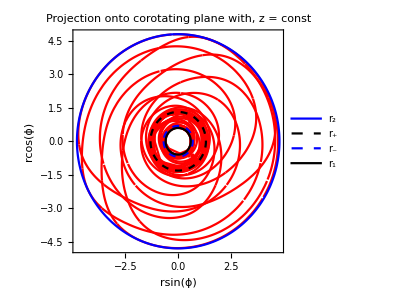
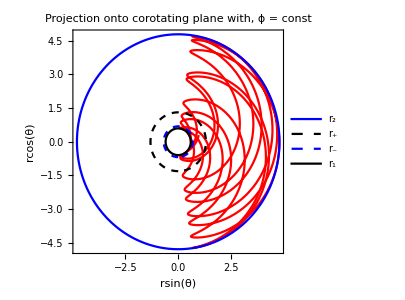

corotatingGenericPlots.pdf

```mathematica
v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]],Re[r[λ]]Cos[Re[ϕ[λ]]]}, {λ,0,20},ImageSize->300, PlotRange->All,PlotLabel-> Style["Projection onto corotating plane with, z = const",Black,14], PlotStyle->Red, MaxRecursion->10,Frame->True,FrameLabel->{ Style["rsin(ϕ)",Black,14], Style["rcos(ϕ)",Black,14]}];
v2 = ParametricPlot[{{r2*Cos[u],r2 Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{r1*Cos[u],r1 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,PlotRange->All,PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotLegends->{ Style["r_2",Black,14], Style["r_+",Black,14], Style["r_-",Black,14], Style["r_1",Black,14]}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{r[λ]*Sin[θ[λ]],r[λ]*Cos[θ[λ]]} , {λ,0,20},ImageSize->300, PlotRange->All,PlotLabel-> Style[ "Projection onto corotating plane with, ϕ = const",Black,14],MaxRecursion->10, PlotStyle->Red,Frame->True,FrameLabel->{ Style["rsin(θ)",Black,14], Style["rcos(θ)",Black,14]}];
Q2 = ParametricPlot[{{r2*Cos[π/2-u],r2 Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{r1*Cos[π/2-u],r1 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->10,PlotLegends->{ Style["r_2",Black,14], Style["r_+",Black,14], Style["r_-",Black,14], Style["r_1",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];
corotatingGenericPlots = Row[{a1,a2}]
Export["corotatingGenericPlots.pdf",Style[corotatingGenericPlots,LineBreakWithin->False],"PDF"]
```

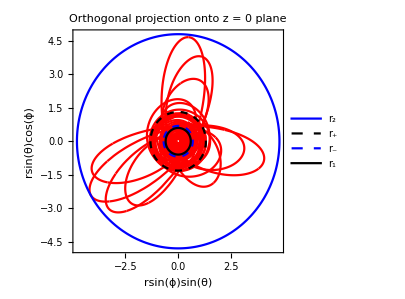
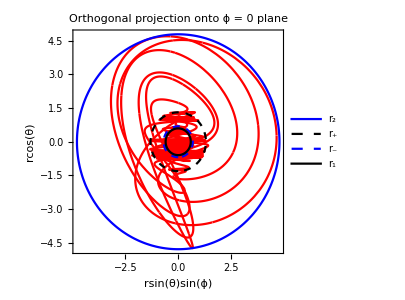
-Graphics--Graphics3D--Graphics-

GenericPlots.pdf

{0.516307,4.87263,2.56869-2.63788 ⅈ,2.56869+2.63788 ⅈ}

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,0,20}, PlotLabel-> Style["3D Spatial Plot",Black,14],ImageSize->300,MaxRecursion->10, PlotStyle->Red,PlotRange->All, AxesLabel->{Style["rsin(ϕ)sin(θ)",Black,12],Style["rsin(θ)cos(ϕ)",Black,12],Style["rcos(θ)",Black,12]}, LabelingSize->30];
P2 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},ImageSize->300,MaxRecursion->4,PlotStyle->{Opacity[1],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
a0 = Show[P1,P2];

v1 = ParametricPlot[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]]}, {λ,0,20},ImageSize->300, PlotRange->All, PlotLabel->Style[ "Orthogonal projection onto z = 0 plane",Black,14], PlotStyle->Red, MaxRecursion->10, Frame->True, FrameLabel->{Style["rsin(ϕ)sin(θ)",Black,14],Style["rsin(θ)cos(ϕ)",Black,14]}];
v2 = ParametricPlot[{{r2*Cos[u],r2 Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{r1*Cos[u],r1 Sin[u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,MaxRecursion->10,PlotRange->All,PlotLegends->{Style["r_2",Black,14],Style["r_+",Black,14],Style["r_-",Black,14],Style["r_1",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a1 = Show[v1,v2];

Q1 = ParametricPlot[{Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]} , {λ,0,20},ImageSize->300, PlotRange->All, PlotStyle->Red,MaxRecursion->10, PlotLabel-> Style["Orthogonal projection onto ϕ = 0 plane",Black,14],Frame->True, FrameLabel->{Style["rsin(θ)sin(ϕ)",Black,14],Style["rcos(θ)",Black,14]}, MaxRecursion->10];
Q2 = ParametricPlot[{{r2*Cos[π/2-u],r2 Sin[π/2-u]},{RP*Cos[π/2-u],RP Sin[π/2-u]},{RM*Cos[π/2-u],RM Sin[π/2-u]},{r1*Cos[π/2-u],r1 Sin[π/2-u]}},{u,-π,π},ImageSize->300,MaxRecursion->12,PlotLegends->{Style["r_2",Black,14],Style["r_+",Black,14],Style["r_-",Black,14],Style["r_1",Black,14]},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}},PlotStyle->{{Blue},{Black,Dashed},{Blue,Dashed}, {Black}}];
a2 = Show[Q1,Q2];


GenericPlots = Row[{a1,a0,a2}]
Export["GenericPlots.pdf",Style[GenericPlots,LineBreakWithin->False],"PDF"]
```

## Radial Flow

### Equations

```mathematica
Λ = z[(4 EllipticK[KZ])/Z2];
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);
RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2))

RIEQUAT  = KerrGeoISSO[a,1]
{ϵEQUAT, LEQUAT, QEQUAT} = Values[KerrGeoConstantsOfMotion[a,RI,0,1]]

RadialInFlowPolarAvg[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( Z2^2/(1-ϵ^2)(1-EllipticE[KZ]/EllipticK[KZ])  ));
RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r )])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L)-a^2 ϵ);
```

3.15804

{0.888442,2.49103,0}

### Analysis and Plots

#### Plots of Flows

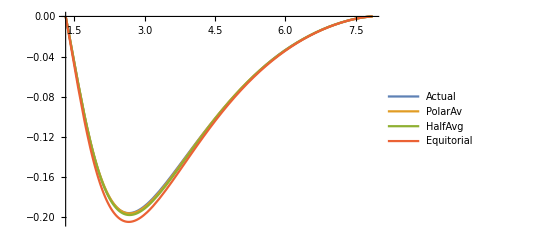

```mathematica
Plot[{RadialInFlowTrue[r],RadialInFlowPolarAvg[r],RadialInFlowHalfAvg[r],RadialInFlowEquitorial[r]},{r,RP,RI}, PlotRange->All,PlotLegends->{"Actual","PolarAv","HalfAvg","Equitorial"}]
```

#### Errors

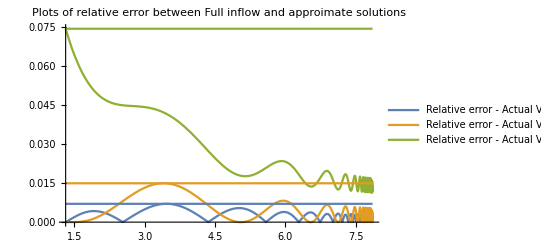

```mathematica
Q1 = Plot[{Abs[(RadialInFlowTrue[r] - RadialInFlowPolarAvg[r])/RadialInFlowTrue[r]] ,Abs[(RadialInFlowTrue[r] - RadialInFlowHalfAvg[r])/RadialInFlowTrue[r]],Abs[(RadialInFlowTrue[r] - RadialInFlowEquitorial[r])/RadialInFlowTrue[r]] },{r,RP,RI-0.001}, PlotRange->All, PlotLabel->"Plots of relative error between Full inflow and approimate solutions",PlotLegends->{"Relative error - Actual Vs PolarAv","Relative error - Actual Vs HalfAvg","Relative error - Actual Vs Equitorial"}];

Max1 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max2 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];
Max3 = NMaximize[{Abs[(RadialInFlowTrue[x] - RadialInFlowEquitorial[x])/RadialInFlowTrue[x]], RP+0.001<=x<=RI-0.001},x][[1]];

Q2 =ParametricPlot[{ {r,Max1},{r,Max2},{r,Max3}},{r,RP,RI}];


Show[Q1,Q2]
```

```mathematica
KerrGeoISSO[0.009,1]
```

5.97057

### MODULEFORM

#### PolarAvgFunc

```mathematica
ErrorModuleFlowPolarAvg[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowPolarAvg[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ + ( Z2^2/(1-ϵ^2)(1-EllipticE[KZ]/EllipticK[KZ])  ));
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowPolarAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### HalfAvg

```mathematica
ErrorModuleFlowHalfAvg[a_,θINC_]:=Module[{param, ϵ, RI ,N=100,, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowHalfAvg[r_]:= (-Sqrt[(ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] - RadialInFlowHalfAvg[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### Equitorial

```mathematica
ErrorModuleFlowEquitorial[a_,θINC_]:=Module[{param, ϵ, N=100, RI, KZ,R4,rValue,L,Q,J,Z1, Z2,RM,RP,M=1, χINC, NMAX 
},
(*FIXME: add stability check but make it possible to turn it off*)
	χINC = Cos[θINC];
	RI = KerrGeoISSO[a,χINC];
	ϵ = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[1]];
	L = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[2]];
	Q = Values[KerrGeoConstantsOfMotion[a,RI,0,χINC]][[3]];
	RM = M-Sqrt[M^2-a^2];
	RP = M+Sqrt[M^2-a^2];
R4 = (a^2 Q)/(J*RI^3);
	KZ = a^2*J(Z1^2/Z2^2);
	J = 1-ϵ^2;
	{Z1,Z2}= {Sqrt[1/2 (1+(L^2+Q)/(a^2 J)-Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])],Sqrt[ (a^2 J)/2 (1+(L^2+Q)/(a^2 J)+Sqrt[(1+(L^2+Q)/(a^2 J))^2-(4 Q)/(a^2 J)])]};
R[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q);


RadialInFlowTrue[r_]:= (-Sqrt[R[r]])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ(1-(Z1 JacobiSN[ (2 Z2 √(r-R4))/(√((1-ϵ^2) (RI-r) (R4-RI)^2))+EllipticK[KZ],KZ])^2));

RadialInFlowEquitorial[r_]:= (-Sqrt[(1-ϵ^2)(RI-r)^3(r)])/(a L +(r^2+a^2)/((r-RP)(r-RM))(ϵ(r^2+a^2)-a L )-a^2 ϵ);
ErrorModuleFLowPolarAvg[x_]:= Abs[(RadialInFlowTrue[x] -RadialInFlowEquitorial[x])/RadialInFlowTrue[x]];
rValue = Table[i,{i,RP+0.01,RI-0.01,(RI-RP)/N}];


ErrorModuleFLowPolarAvgList = Map[ErrorModuleFLowPolarAvg, rValue];

 NMAX = Max[ErrorModuleFLowPolarAvgList ];

 Return[NMAX];
	]
```

#### The matrices

```mathematica
<<KerrGeodesics`
n = 20;

a = Table[i, {i,0.01,0.99,0.999/n}];
 θINC =Table[i, {i,0,π,π/(2n)}];

f[x_,y_]:= {x,y}

aMatrixFunc[x_] :=x[[1]];
 aMF=Map[aMatrixFunc,Outer[f,a,  θINC ],{2}];

θMatrixFunc[x_] :=x[[2]];
 θMF=Map[θMatrixFunc,Outer[f,a,  θINC  ],{2}];

ErrorPolarAvgFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowPolarAvg[x[[1]],x[[2]]]};
ErrorPolarAvgMF = Map[ErrorPolarAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorHalfAvgFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowHalfAvg[x[[1]],x[[2]]]};
ErrorHalfAvgMF = Map[ErrorHalfAvgFunction,Outer[f,a,  θINC  ],{2}];

ErrorEquatorFunction[x_]:={Cos[x[[2]]],x[[1]],ErrorModuleFlowEquitorial[x[[1]],x[[2]]]};
ErrorEquatorMF = Map[ErrorEquatorFunction,Outer[f,a,  θINC  ],{2}];
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

#### Trash

```mathematica
ϵMatrixFunc[x_] :=KerrGeoEnergy[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 ϵMF=Map[ϵMatrixFunc,Outer[f,a, χINC ],{2}];

LMatrixFunc[x_] :=KerrGeoAngularMomentum[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 LMF=Map[LMatrixFunc,Outer[f,a, χINC ],{2}];

QMatrixFunc[x_] :=KerrGeoCarterConstant[x[[1]], KerrGeoISSO[x[[1]],x[[2]]],0,x[[2]]];
 QMF=Map[QMatrixFunc,Outer[f,a, χINC ],{2}];

RIMatrixFunc[x_] := KerrGeoISSO[x[[1]],x[[2]]];
 RIMF=Map[RIMatrixFunc,Outer[f,a, χINC ],{2}];


RPMF = 1+Sqrt[1-aMF^2];
RMMF = 1-Sqrt[1-aMF^2];

R4 =(a^2 QMF)/((1-ϵMF^2)*RIMF^3) ;


Z1MF= Sqrt[1/2 (1+(LMF^2+QMF)/(aMF^2  (1-ϵMF^2))-Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2  (1-ϵMF^2))])];

Z2MF= Sqrt[ (aMF^2 (1-ϵMF^2))/2 (1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2))+Sqrt[(1+(LMF^2+QMF)/(aMF^2 (1-ϵMF^2)))^2-(4 QMF)/(aMF^2 (1-ϵMF^2))])];

KZMF = aMF^2*(1-ϵMF^2)(Z1MF^2/Z2MF^2);


rn = 10;
rValuesFunction[x_] := Table[i, {i,(1+Sqrt[1-x[[1]]^2]),KerrGeoISSO[x[[1]],x[[2]]], (KerrGeoISSO[x[[1]],x[[2]]]-(1+Sqrt[1-x[[1]]^2]))/rn}]
rMF=Map[rValuesFunction,Outer[f,a, χINC ],{2}];
```

### ContourPlotOverParamaterSpace

```mathematica
range
```

{-11,11}

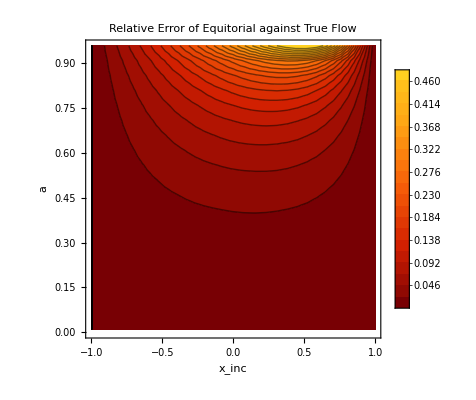
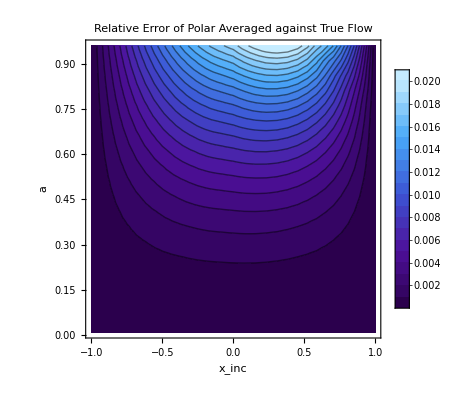

ContourFLows.pdf

```mathematica
range={0,0.5};
c1=ListContourPlot[Flatten[ErrorEquatorMF,1],PlotLegends->Automatic,FrameLabel->{Style["x_inc",Black,16],Style["a",Black,16]},ImageSize->400,PlotRange->{0,0.5},Contours->20,ColorFunction->ColorData[{"SolarColors",{0,0.5}}],ColorFunctionScaling->False,PlotLabel->Style["Relative Error of Equitorial against True Flow",Black,16]];
c2=ListContourPlot[Flatten[ErrorPolarAvgMF,1],PlotLegends->Automatic,ImageSize->400,Contours->20,ColorFunction->ColorData[{"DeepSeaColors",{0,0.02}}],ColorFunctionScaling->False, PlotLabel->Style["Relative Error of Polar Averaged against True Flow",Black,16],FrameLabel->{Style["x_inc",Black,16],Style["a",Black,16]}];
pp = Row[{c1,c2}]


Export["ContourFLows.pdf",Style[pp,LineBreakWithin->False],"PDF"]
```

## Testing Solutions

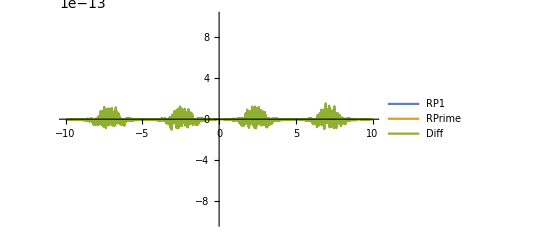

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

Plot[{RPoly1[r[λ]], (r'[λ])^2, (r'[λ])^2- RPoly1[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.0000000000010,0.0000000000010}}]
```

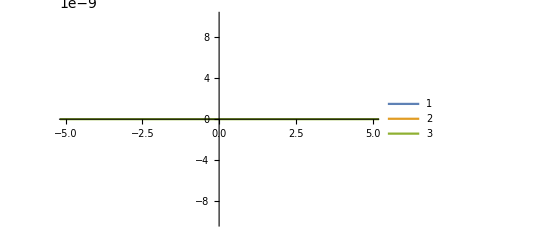

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ}, PlotRange->{{-5,5},{-0.000000010,0.000000010}}]
```

```mathematica
|
```

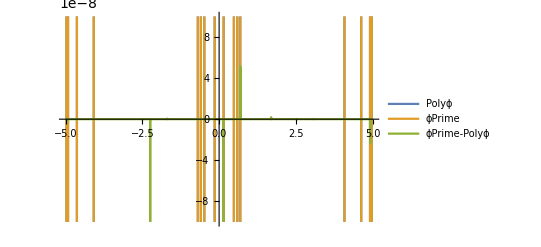

1.67166+6.11941×10^-15 ⅈ

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->{{-5,5},{-0.00000010,0.00000010}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
ϕ'[3]
```

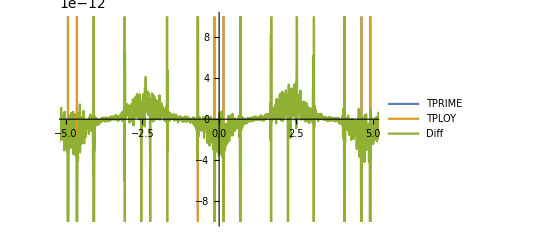

```mathematica
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[t'[λ]],TPoly[λ],Re[t'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}, PlotRange->{{-5,5},{-0.000000000010,0.000000000010}}]
```

```mathematica
t'[3]
```

(12.6154+1.53789×10^-14 ⅈ)+0.9 (7.29546+(4.06972-6.66134×10^-16 ⅈ) Re'[-0.982129-0.600977 ⅈ])

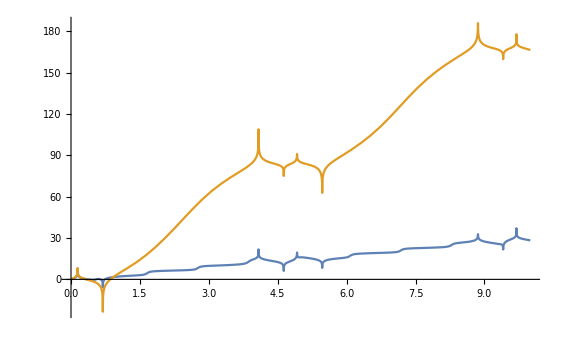

```mathematica
Plot[{Re[ϕ[λ]], Re[t[λ]]},{λ,0,10}]
```